## Morse Potential for HCL

### electron charge

```mathematica
ee= 1.60217646×10^-19
```

1.60218×10^-19

### equil dist in nm

```mathematica
re=0.1275
```

0.1275

### Dissociation energy in eV

```mathematica
V0=4.436
```

4.436

### Reduced Mass of HCL in kg

```mathematica
Mp=1.62747 10^-27
```

1.62747×10^-27

### Reduced mass in energy units - eV

```mathematica
muE=Mp (299792458)^2/ee
```

9.12944×10^8

### Speed of light is 300 nm per femtosecond

```mathematica
c=(299792458. 10^-15/10^-9)
```

299.792

### Reduced mass in mass units

```mathematica
mu = muE/c^2
```

10157.9

### hbar

```mathematica
hbar = 1.05457148×10^-34
```

1.05457×10^-34

### hbar in nmfs units

```mathematica
hbarNMFS = hbar/(ee 10^-15)
```

0.658212

### width in nm^-1

```mathematica
beta = 18.1181
```

18.1181

### Potential function

```mathematica
VM[V0_,beta_,re_,r_]:=V0(Exp[-2 beta (r-re)]-2 Exp[-beta (r-re)])
```

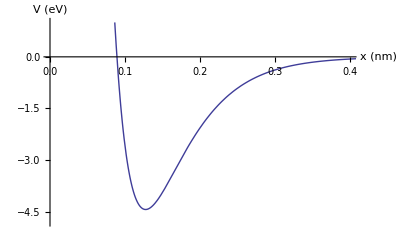

```mathematica
pot=Plot[VM[V0,beta,re,r],{r,0.0001,1},PlotRange->{{0,0.4},{-4.8,1}},AxesLabel->{"x (nm)","V (eV)"}]
```

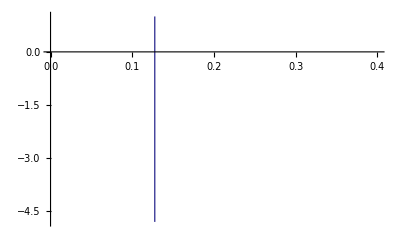

```mathematica
min =ListLinePlot[{{re,-4.8},{re,1}},PlotRange->{{0,0.4},{-4.8,1}}]
```

### Make the solution

```mathematica
nu = Sqrt[(8 mu V0)/(beta^2 hbarNMFS^2) ]
```

50.3459

### Spectrum

```mathematica
En[nn_]:=-(beta^2 hbarNMFS^2)/mu(nu-2nn-1)^2/8
```

```mathematica
Table[En[nn]-En[nn+1],{nn,0,25}]
```

{-0.338441,-0.32444,-0.31044,-0.296439,-0.282438,-0.268437,-0.254436,-0.240435,-0.226435,-0.212434,-0.198433,-0.184432,-0.170431,-0.15643,-0.14243,-0.128429,-0.114428,-0.100427,-0.0864262,-0.0724253,-0.0584245,-0.0444237,-0.0304228,-0.016422,-0.00242116,0.0115797}

```mathematica
ps=Table[{{0,En[nn]},{1,En[nn]}},{nn,0,25}]
```

{{{0,-4.26153},{1,-4.26153}},{{0,-3.92309},{1,-3.92309}},{{0,-3.59865},{1,-3.59865}},{{0,-3.28821},{1,-3.28821}},{{0,-2.99177},{1,-2.99177}},{{0,-2.70933},{1,-2.70933}},{{0,-2.44089},{1,-2.44089}},{{0,-2.18646},{1,-2.18646}},{{0,-1.94602},{1,-1.94602}},{{0,-1.71959},{1,-1.71959}},{{0,-1.50715},{1,-1.50715}},{{0,-1.30872},{1,-1.30872}},{{0,-1.12429},{1,-1.12429}},{{0,-0.953858},{1,-0.953858}},{{0,-0.797428},{1,-0.797428}},{{0,-0.654998},{1,-0.654998}},{{0,-0.526569},{1,-0.526569}},{{0,-0.412142},{1,-0.412142}},{{0,-0.311715},{1,-0.311715}},{{0,-0.225288},{1,-0.225288}},{{0,-0.152863},{1,-0.152863}},{{0,-0.0944385},{1,-0.0944385}},{{0,-0.0500149},{1,-0.0500149}},{{0,-0.019592},{1,-0.019592}},{{0,-0.00317003},{1,-0.00317003}},{{0,-0.00074887},{1,-0.00074887}}}

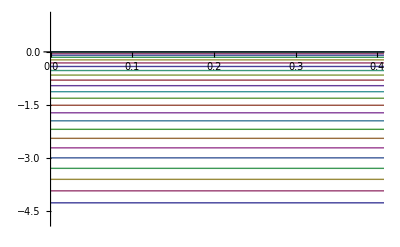

```mathematica
levels=ListLinePlot[ps,PlotRange->{{0,0.4},{-4.8,1}}]
```

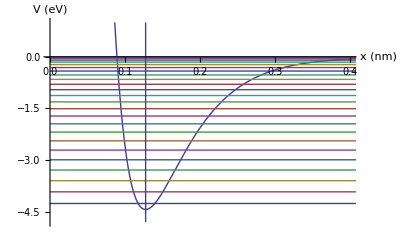

```mathematica
Show[pot,levels,min]
```

```mathematica
Nm[nu_,nn_]:=Sqrt[(beta (nu-2nn-1)Gamma[nn+1])/Gamma[nu-nn]]
```

```mathematica
y[nu_,beta_,x_]:=nu Exp[-beta x]
```

```mathematica
sE[nn_]:=Sqrt[(-2 mu En[nn])/(beta^2 hbarNMFS^2)]
```

```mathematica
Clear[s]
```

```mathematica
s[nn_]:=(nu-1)/2-nn
```

```mathematica
Table[{s[nn],s2[nn]},{nn,0,25}]
```

{{24.6729,s2[0]},{23.6729,s2[1]},{22.6729,s2[2]},{21.6729,s2[3]},{20.6729,s2[4]},{19.6729,s2[5]},{18.6729,s2[6]},{17.6729,s2[7]},{16.6729,s2[8]},{15.6729,s2[9]},{14.6729,s2[10]},{13.6729,s2[11]},{12.6729,s2[12]},{11.6729,s2[13]},{10.6729,s2[14]},{9.67293,s2[15]},{8.67293,s2[16]},{7.67293,s2[17]},{6.67293,s2[18]},{5.67293,s2[19]},{4.67293,s2[20]},{3.67293,s2[21]},{2.67293,s2[22]},{1.67293,s2[23]},{0.67293,s2[24]},{-0.32707,s2[25]}}

```mathematica
PsiB[x_,nn_]:=Nm[nu,nn]Exp[-y[nu,beta,x-re]/2] y[nu,beta,x-re]^s[nn] LaguerreL[nn,2s[nn],y[nu,beta,x-re]]
```

```mathematica
st[nn_]:=Plot[PsiB[x,nn]/12+En[nn],{x,0.0001,1},PlotRange->{{0,0.4},{-4.8,1}}]
```

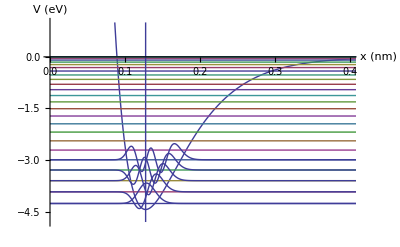

```mathematica
Show[pot,levels,st[0],st[1],st[2],st[3],st[4],min]
```

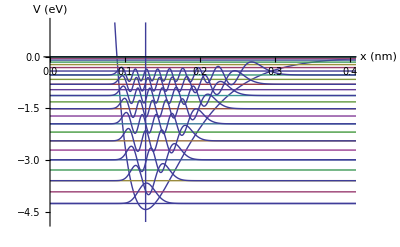

```mathematica
Show[pot,levels,st[0],st[2],st[4],st[6],st[8],st[10],st[12],st[14],st[16],min]
```

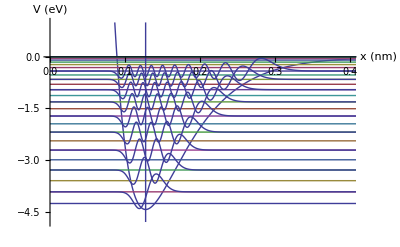

```mathematica
Show[pot,levels,st[1],st[3],st[5],st[7],st[9],st[11],st[13],st[15],st[17],min]
```

```mathematica
Table[En[nn],{nn,0,25}]
```

{-4.26153,-3.92309,-3.59865,-3.28821,-2.99177,-2.70933,-2.44089,-2.18646,-1.94602,-1.71959,-1.50715,-1.30872,-1.12429,-0.953858,-0.797428,-0.654998,-0.526569,-0.412142,-0.311715,-0.225288,-0.152863,-0.0944385,-0.0500149,-0.019592,-0.00317003,-0.00074887}

## Scattering solutions

### The energy of a free particle with wavelength equal to 1/β is 0.007 eV.

```mathematica
(beta^2 hbarNMFS^2)/(2 mu)
```

0.00700042

### Looking at the Mathematica documentation on 1F1 - that its a soln of Kummers eqn in particular, this form is correct up to the constants

```mathematica
PsiPlus[x_,k_]:=Exp[-y[nu,beta,x]/2](y[nu,beta,x])^(I k)Hypergeometric1F1[I k+(1-nu)/2,2I k+1,y[nu,beta,x]]
```

```mathematica
PsiMinus[x_,k_]:=Exp[-y[nu,beta,x]/2](y[nu,beta,x])^(-I k)Hypergeometric1F1[-I k+(1-nu)/2,-2I k+1,y[nu,beta,x]]
```

### You have to combine these with the right coeff so that the scattering solution decays correctly for negative x where the potential diverges

```mathematica
CC[k_,nu_]:=- (Gamma[2 I k +1]Gamma[-I k +(1-nu)/2])/(Gamma[-2 I k +1]Gamma[I k +(1-nu)/2])
```

```mathematica
PsiS[x_,k_]:=PsiPlus[x,k]+CC[k,nu]PsiMinus[x,k]
```

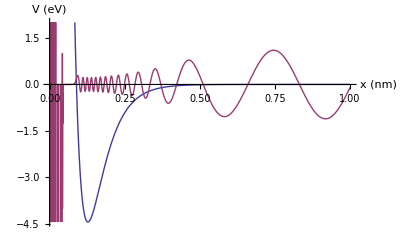

```mathematica
Plot[{VM[V0,beta,re,x],Re[PsiS[x-re,1]]},{x,0,1},PlotRange->{{0,1},{2,-V0}},AxesLabel->{"x (nm)","V (eV)"}]
```

```mathematica
nu beta/2
```

456.086

## Make sampled versions for output and comparison - first do bound states

### Discretization is 0.001 nm = 1pm for all 11 reportable simulations - which are discretized with either 2048, 4096 or 8192 points

```mathematica
dx=0.001
```

0.001

```mathematica
NN1=2048
```

2048

```mathematica
NN2=4096
```

4096

```mathematica
NN3=8196
```

8196

```mathematica
PsiBN1[nl_]:=Table[PsiB[dx nn,nl],{nn,0,NN1-1}];
```

```mathematica
PsiBN2[nl_]:=Table[PsiB[dx nn,nl],{nn,0,NN2-1}];
```

```mathematica
PsiBN3[nl_]:=Table[PsiB[dx nn,nl],{nn,0,NN3-1}];
```

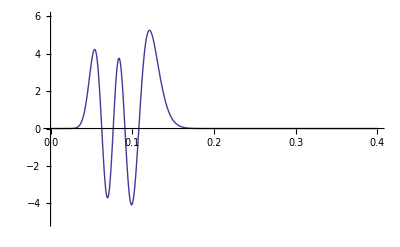

```mathematica
Plot[Re[PsiB[x,4]],{x,0,0.4},PlotRange->{{0,0.4},{-5,6}}]
```

```mathematica
NN1 dx
```

2.048

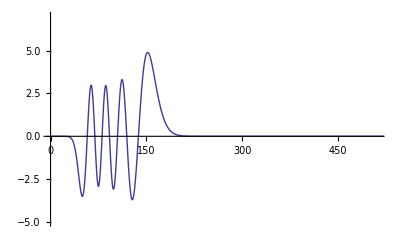

```mathematica
ListLinePlot[PsiBN1[7],PlotRange->{{0,NN1/4},{-5,7}}]
```

```mathematica
Directory[]
```

/Users/plove

```mathematica
SetDirectory["/Users/plove/Documents/RESEARCH/Current/QLGPRA/Morseexact"]
```

/Users/plove/Documents/RESEARCH/Current/QLGPRA/Morseexact

```mathematica
Directory[]
```

/Users/plove/Documents/RESEARCH/Current/QLGPRA/Morseexact

```mathematica
expfunc[x_]:=Null
```

### Ground state

```mathematica
data0=Chop[Table[NumberForm[PsiB[dx nn,0],10,ExponentFunction->expfunc],{nn,0,NN1-1}]];
```

```mathematica
fname="Bound_0_2048.txt"
```

Bound_0_2048.txt

```mathematica
f=OpenWrite[fname, BinaryFormat->True]
```

OutputStream[Bound_0_2048.txt,159]

```mathematica
Do[WriteString[f,data0[[ii]],"\n"],{ii,1,2048}]
```

```mathematica
Close[fname]
```

Bound_0_2048.txt

### 1st state

```mathematica
data1=Chop[Table[NumberForm[PsiB[dx nn,1],10,ExponentFunction->expfunc],{nn,0,NN1-1}]];
```

```mathematica
fname="Bound_1_2048.txt"
```

Bound_1_2048.txt

```mathematica
"Bound_1_2048.txt"
```

Bound_1_2048.txt

```mathematica
f=OpenWrite[fname]
```

OutputStream[Bound_1_2048.txt,172]

```mathematica
Do[WriteString[f,data1[[ii]],"\n"],{ii,1,2048}]
```

```mathematica
Close[fname]
```

Bound_1_2048.txt

### Automate

```mathematica
fnamen[n_]:=StringJoin["Bound_" ,ToString[n],"_2048.txt"]
```

```mathematica
fnamep[n_]:=StringJoin["Bound_" ,ToString[n],"_4096.txt"]
```

```mathematica
fnameq[n_]:=StringJoin["Bound_" ,ToString[n],"_8192.txt"]
```

```mathematica
fnamen[0]
```

Bound_0_2048.txt

```mathematica
CompoundExpression[jj=1;data=Chop[Table[NumberForm[PsiB[dx nn,jj],10,ExponentFunction->expfunc],{nn,0,NN1-1}]];fname=fnamen[jj];f=OpenWrite[fname];Do[WriteString[f,data1[[ii]],"\n"],{ii,1,2048}];Close[fname]]
```

Bound_1_2048.txt

### Do all the 2048 ones

```mathematica
Do[CompoundExpression[jj=pp;data=Chop[Table[NumberForm[PsiB[dx nn,jj],10,ExponentFunction->expfunc],{nn,0,NN1-1}]];fname=fnamen[jj];f=OpenWrite[fname];Do[WriteString[f,data[[ii]],"\n"],{ii,1,2048}];Close[fname]],{pp,0,17}]
```

### Do all the 4096 ones

```mathematica
Do[CompoundExpression[jj=pp;data=Chop[Table[NumberForm[PsiB[dx nn,jj],10,ExponentFunction->expfunc],{nn,0,NN2-1}]];fname=fnamep[jj];f=OpenWrite[fname];Do[WriteString[f,data[[ii]],"\n"],{ii,1,4096}];Close[fname]],{pp,0,17}]
```

### Do all the 8192 ones

```mathematica
Do[CompoundExpression[jj=pp;data=Chop[Table[NumberForm[PsiB[dx nn,jj],10,ExponentFunction->expfunc],{nn,0,NN3-1}]];fname=fnameq[jj];f=OpenWrite[fname];Do[WriteString[f,data[[ii]],"\n"],{ii,1,8192}];Close[fname]],{pp,0,17}]
```

## Now do scattering states - harder as must get continuum

### dx sets the upper momentum cutoff - way above the free particle limit by about 10x

```mathematica
kmax =Pi/dx
```

3141.59

### Number of points sets difference between adjacent momenta

```mathematica
dk1=Pi/(NN1 dx)
```

1.53398

```mathematica
dk2=Pi/(NN2 dx)
```

0.76699

```mathematica
dk3  =Pi/(NN3 dx)
```

0.383308

### Lets make the k value tables - k in inverse nanometers

```mathematica
ks1=Flatten[{Table[-dk1 nn,{nn,NN1/2,1,-1}],Table[dk1 nn,{nn,1,NN1/2,1}]}];
```

```mathematica
ks2=Flatten[{Table[-dk2 nn,{nn,NN2/2,1,-1}],Table[dk2 nn,{nn,1,NN2/2,1}]}];
```

```mathematica
ks3=Flatten[{Table[-dk3 nn,{nn,NN3/2,1,-1}],Table[dk3 nn,{nn,1,NN3/2,1}]}];
```

```mathematica
Length[ks1]
```

2048

```mathematica
Plot[{VM[V0,beta,re,x],Re[PsiS[x-re,1]]},{x,0,1},PlotRange->{{0,1},{2,-V0}},AxesLabel->{"x (nm)","V (eV)"}]
```

### Here's the scattering state with k=beta

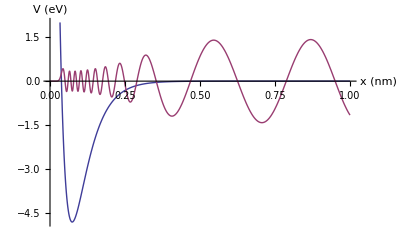

### Here's the scattering state with k = dk1

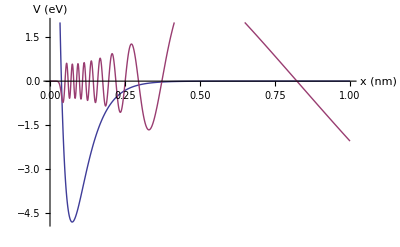

```mathematica
Plot[{VM[V0,beta,re,x],5Re[PsiS[x-re,dk1/beta]]},{x,0,1},PlotRange->{{0,1},{2,-V0}},AxesLabel->{"x (nm)","V (eV)"}]
```

### Here's the scattering state with k = dk2

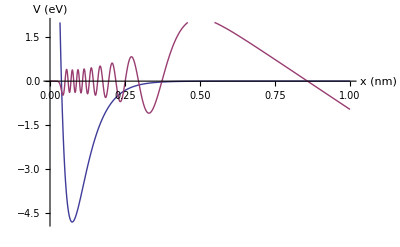

```mathematica
Plot[{VM[V0,beta,re,x],10Re[PsiS[x-re,dk2/beta]]},{x,0,1},PlotRange->{{0,1},{2,-V0}},AxesLabel->{"x (nm)","V (eV)"}]
```

### Here's the scattering state with k = dk3

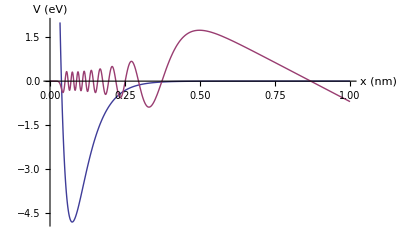

```mathematica
Plot[{VM[V0,beta,re,x],30Re[PsiS[x-re,dk3/beta]]},{x,0,1},PlotRange->{{0,1},{2,-V0}},AxesLabel->{"x (nm)","V (eV)"}]
```

## Conversion to velocity

### Wavevector of packet with energy equal to well depth

```mathematica
nu/2 beta
```

340.094

```mathematica
ptest=hbarNMFS nu/2 beta
```

223.854

```mathematica
ptest/mu
```

0.0428852

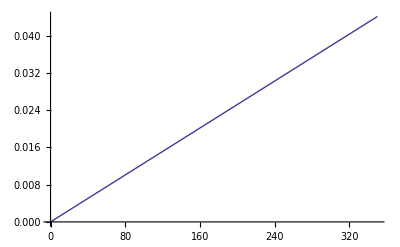

```mathematica
Plot[hbarNMFS k/mu,{k,0,350}]
```

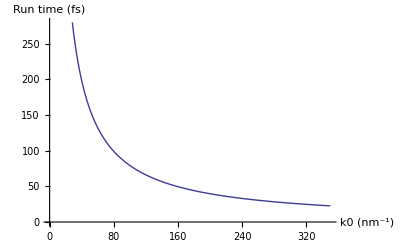

```mathematica
Plot[1/(hbarNMFS k/mu),{k,0,350},PlotRange->{{0,350},{0,280}},AxesLabel->{"k0 (nm^-1)","Run time (fs)"}]
```

```mathematica
3/4 {10,12,15}//N
```

{7.5,9.,11.25}